```mathematica
ClearAll["Global`*"];
(* The steady state function and some good values for Subscript[T, 1e] and Subscript[T, 1n] *)
physicalTimes={t1e->0.03,t1n->1.5*60*60};
pssnPhysical[a_,b_,s_,c_]=(c t1n(b-a))/(t1e(2+2s+a+b)+c t1n(a+s a+b+s b+2a b))/.physicalTimes;

(* Try to model the steady state as a function of frequency *)
(* Here are a list of distributions to use in getting α,β in terms of frequency *)
gaussian[m_,s_,x_]=PDF[NormalDistribution[m,s],x];
cauchy[m_,s_,x_]=PDF[CauchyDistribution[m,s],x];
studentT2[m_,s_,x_]=PDF[StudentTDistribution[m,s,2],x];
studentT3[m_,s_,x_]=PDF[StudentTDistribution[m,s,3],x];
dist1[m_,s_,x_]=Exp[-Abs[(x-m)/s]];
dist21[m_,s_,x_]=gaussian[m-s,s,x]+gaussian[m+s,s,x];
dist22[m_,s_,x_]=gaussian[m-s,s/2,x]+gaussian[m+s,s/2,x];
constant[m_,s_,x_]=1;
(* Choose distribution here *)
distribution=gaussian;
sDistribution=gaussian;
(* Compute alpha, beta distributions *)
alphaDist[a_,m2_,s_,x_]=a distribution[m2,s,x];
betaDist[a_,m1_,s_,x_]=a distribution[m1,s,x];
sDist[as_,ms_,ss_,x_]=as sDistribution[ms,ss,x];

(* The complete equations in terms of the polarizations Subscript[P, n], Subscript[P, e], and Subscript[Q, n] *)
pn0=0;
pe0=-1;
ϕ1=0;
ϕ2=0;
ω1=1/t1e;
θ=(2c t1e)/t1n;
σ=0;
peDot=ω1(α(-4/3 pe[t]+pn[t]+1/3 pe[t]qn[t])+β(-4/3 pe[t]-pn[t]+1/3 pe[t]qn[t])-2s pe[t]+σ((2/3 qn[t]-8/3)(pe[t]-pe0)+2pn0 pe[t]pn[t])-2(pe[t]-pe0));
pnDot=ω1 c(α(2/3 pe[t]-1/2 pn[t]-1/6 pe[t]qn[t])+β(-2/3 pe[t]-1/2 pn[t]+1/6 pe[t]qn[t])+θ(-pn[t]-1/3 pn0 qn[t]+4/3 pn0)+σ(-pe0 pe[t]pn[t]-pn[t]-1/3 pn0 qn[t]+4/3 pn0))+ω1 ϕ1(4/3 pn0-1/3 pn0 qn[t]-pn[t])+ω1 ϕ2(4/3 pn0+2/3 pn0 qn[t]-2pn[t]);
qnDot=ω1 c(α(3/2 pe[t]pn[t]-3/2 qn[t])+β(-3/2 pe[t]pn[t]-3/2 qn[t])+θ(3pn0 pn[t]-3qn[t])+σ(3pe0 pe[t]qn[t]+3pn0 pn[t]-3qn[t]))+ϕ1 ω1(3pn0 pn[t]-3qn[t]);
eqns={pe'[t]==peDot,pn'[t]==pnDot,qn'[t]==qnDot,
pe[0]==-1,pn[0]==0,qn[0]==0};
(* Try to get steady state *)
steadySol=Solve[{peDot==0,pnDot==0,qnDot==0},{pn[t],pe[t],qn[t]}];
pnSteady=pn[t]/.steadySol[[1]];
pssnPhysical[α_,β_,s_,c_]=pnSteady/.physicalTimes/.{α->α,β->β,s->s,c->c};
(* Set up steady state function *)
pssnDistribution[a_,s_,m1_,m2_,as_,ms_,ss_,c_,x_]=pssnPhysical[alphaDist[a,m2,s,x],betaDist[a,m1,s,x],sDist[as,ms,ss,x],c];

(* The real steady state data *)
realDataList={{140,0.8},{140.04,1.2},{140.2,3.3},{140.4,-3.0},{140.5,-0.5}};
(* Normalized real data *)
maxSteadyState=0.9;
realDataListAdj=Map[Function[list,{list[[1]],list[[2]]/(3.3/maxSteadyState)}],realDataList];
(*
(* Calculate a fit for the various parameters *)
bestFit=FindFit[realDataListAdj,{pssnDistribution[a,s,m1,m2,as,ms,ss,c,x],
{0≤a≤5,0.001≤s≤1,140.2≤m1≤140.6,140.2≤m2≤140.6,0≤as≤5,140≤ms≤141,0.001≤ss≤1,0.01*^-4≤c≤100*^-4}},
{a,s,m1,m2,as,ms,ss,c},x]

(* Show some useful plots *)
steadyStatePlot=Show[ListPlot[realDataListAdj],Plot[pssnDistribution[a,s,m1,m2,as,ms,ss,c,x]/.bestFit,{x,140,140.8}],
PlotRange->{{140,140.8},{-1,1}},
ImageSize->Large,
PlotLabel->"Actual steady state vs fit"]
Export["steadystateplot.png",steadyStatePlot]
(* Plot α and β vs frequency *)
alphaBetaPlot=Plot[{alphaDist[a,m2,s,x]/.bestFit,betaDist[a,m1,s,x]/.bestFit},{x,140,140.8},
PlotRange->All,ImageSize->Large,PlotLegends->{"α","β"},
PlotLabel->"Calculated α, β vs frequency"]
Export["alphabetaplot.png",alphaBetaPlot]
(* Plot s vs frequency *)
Plot[sDist[as,ms,ss,x]/.bestFit,{x,140,140.8},
PlotRange->All,ImageSize->Large,PlotLegends->{"s"},
PlotLabel->"Calculated s vs frequency"]
*)
```

$Aborted

Part::partd: Part specification steadySol⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {steadySol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification steadySol⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {steadySol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{a→0.548868,s→0.0873088,m1→140.286,m2→140.468,as→1.70729×10^-6,ms→140.46,ss→0.673762,c→0.00030894}

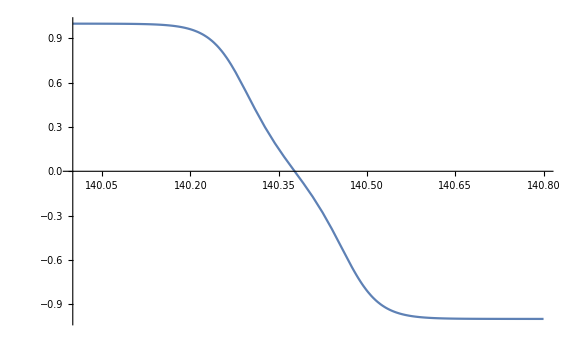

```mathematica
fitHalf={a->0.5488677207924655,s->0.08730876348721682,m1->140.28593970066632,m2->140.46809801922723,as->1.707287796317838*^-6,ms->140.45951191300546,ss->0.673761649746447,c->0.0003089404346889927}
Plot[pssnDistribution[a,s,m1,m2,as,ms,ss,c,x]/.fitHalf,{x,140,140.8},
PlotRange->All,ImageSize->Large]
```